```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/mgreen/GitHub Clones/rcDataLogger/CalibratePitot

```mathematica
data=Import["T1.TXT","CSV"];
```

```mathematica
threadData=Dataset[Map[AssociationThread[First[data],#]&,Rest[data]]]
```

Dataset[<>]

```mathematica
TenMPH=Normal@threadData[Select[#Airspeed==10&]][[All,1]];
TwentyMPH=Normal@threadData[Select[#Airspeed==20&]][[All,1]];
ThirtyMPH=Normal@threadData[Select[#Airspeed==30&]][[All,1]];
FortyMPH=Normal@threadData[Select[#Airspeed==40&]][[All,1]];
FiftyMPH=Normal@threadData[Select[#Airspeed==50&]][[All,1]];
```

```mathematica
allData={TenMPH,TwentyMPH,ThirtyMPH,FortyMPH,FiftyMPH};
```

```mathematica
ten=Sort@allData[[1]];
twenty=Sort@allData[[2]];
thirty=Sort@allData[[3]];
forty= Sort@allData[[4]];
fifty=Sort@allData[[5]];
```

```mathematica
allDataSorted={ten,twenty,thirty,forty,fifty};
```

```mathematica
Summary[list0_]:=Module[{list=list0,val},
val=<||>;
AppendTo[val,<|"Mean"->Mean[list]|>];
AppendTo[val,<|"Median"->Median[list]|>];
AppendTo[val,<|"Variance"->Variance[list]|>];
AppendTo[val,<|"Standard Deviation"->StandardDeviation[list]|>];
AppendTo[val,<|"Min"->Min[list]|>];
AppendTo[val,<|"Max"->Max[list]|>];
AppendTo[val,<|"n"->Length[list]|>];
Dataset[val]
]
```

```mathematica
Summary/@allDataSorted//TableForm;
averageValues=Mean[#]&/@allDataSorted
```

{910.828,925.307,951.833,1006.57,1025.26}

```mathematica
data={{10,averageValues[[1]]},
{20,averageValues[[2]]},
{30,averageValues[[3]]},
{40,averageValues[[4]]},
{50,averageValues[[5]]}
}
```

{{10,910.828},{20,925.307},{30,951.833},{40,1006.57},{50,1025.26}}

```mathematica
model=LinearModelFit[data,x,x]
```

FittedModel[870.924+3.10115 x]

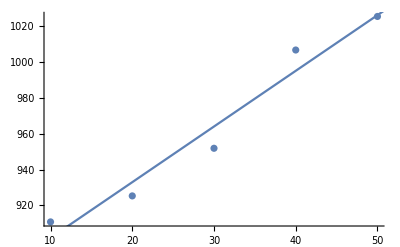

```mathematica
Show[ListPlot[data],Plot[model[x],{x,0,55}]]
```